```mathematica
l=L*as*b0;
```

```mathematica
unprime = (L/(2*Pi*b0*l)*((1-2*l)*Log[1-2*l]-(2-2*l)*Log[1.-l
])//Simplify)/.L:>Log[1/tau]
prime =( D[ (L/(2*Pi*b0*l)*((1-2*l)*Log[1-2*l]-(2-2*l)*Log[1-l
])//Simplify),L]//Simplify)/.L:>Log[1/tau]
```

((0.159155-0.31831 as b0 log(1/tau)) log(1.-2. as b0 log(1/tau))+(0.31831 as b0 log(1/tau)-0.31831) log(1.-1. as b0 log(1/tau)))/(as b0^2)

(log(1-as b0 log(1/tau))-log(1-2 as b0 log(1/tau)))/(π b0)

```mathematica
Log[1/1]
```

0

```mathematica
NIntegrate[prime*Exp[-unprime]/.as:>0.1/.b0:>11/3,{tau,0,1}]
```

0.0226358-0.0534562 ⅈ

```mathematica
NIntegrate[prime*Exp[-unprime]unprime/.as:>0.1/.b0:>11/3,{tau,0.00000001,0.99999}]
NIntegrate[prime*Exp[-unprime]/.as:>0.1/.b0:>11/3,{tau,0.00000001,0.99999}]
```

-0.00562186+0.00140935 ⅈ

0.0226356-0.0534861 ⅈ

```mathematica
((((1-as b0 L)^(1/(b0 π)) (Log[-as b0 L]))/(b0 π)//FullSimplify)/.as:>0.01/.b0:>11/3//Simplify)/.L:>100000000000
```

11.9591+5.26083 ⅈ

ConditionalExpression[1-(1-(2 as b0)/(a+b))^(1/(π b0)),Re((a+b)/(as b0))>2∨Re((a+b)/(as b0))<0∨(a+b)/(as b0)∉ℝ]

```mathematica
-l Integrate[x Exp[-l x],x]
```

(ⅇ^(-l x) (l x+1))/l

```mathematica
l=as0*b0*L
```

as0 b0 L

```mathematica
tt[as0_,b0_,l_]:=-1./(Pi*b0)*Log[1.-2.*l]
```

```mathematica
rp=2.*CF(1./b*(tt[as0,b0,L/a]-tt[as0,b0,L/(a+b)]))
```

(2. C_F ((0.31831 log(1.-(2. L)/(a+b)))/b0-(0.31831 log(1.-(2. L)/a))/b0))/b

```mathematica
rpp[L_]:=rp/.a:>1/.b:>1/.b0:>11/3/.CF:>4/3
```

```mathematica
(-EulerGamma*rpp[L]-Log[Gamma[(1.+rpp[L])]])//Series[#,{L,Infinity,2}]&//Normal//FullSimplify
```

1/L^2((-0.0230373 L-0.0347465) L+6.77626×10^-21 log^8(-1. L)-9.48677×10^-20 log^6(-1. L)+1.30104×10^-18 log^4(-1. L)+(1.73472×10^-18-1.73472×10^-18 L) log^2(-1. L)-0.0403662)

```mathematica
Log[1-x]//Series[#,{x,Infinity,2}]&
```

log(-x)-1/x-1/(2 x^2)+O((1/x)^3)

```mathematica
-EulerGamma*r-Log[Gamma[(1.+r)]]//Series[#,{r,0,2}]&
```

-0.822467 r^2+O(r^3)

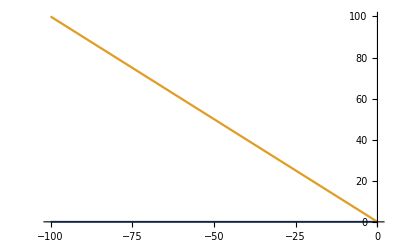

```mathematica
Plot[{-EulerGamma*rpp[L]-Log[Gamma[(1.+rpp[L])]],-L},{L,-100,0}]
```